# Le crible de Matiiassevitch

## UPEC, Paris.

Guillaume Saës (guillaume.saes@u-pec.fr)

## Énoncé

C’est un exercice de programmation et d’observation mathématiques.
Vous devez être autonome et savoir utiliser l’aide Mathematica afin de réussir.

### 1. Illustrer la parabole de la fonction carrée sur un graphique

On pourra utiliser la fonction “Plot” vu précédemment.

### 2. Placer les points de coordonnées entières sur la parabole entre -5 et 5 (Par exemple : (-2,4) ou (5,25))

On pourra s’aider de la fonction “Point” et “Table”.
Aidez-vous de l’aide Mathematica qui affiche ceci dans ses applications :
Plot[Sin[x],{x,0,5Pi},Epilog→{PointSize[Medium],Point[Table[{k Pi,0},{k,0,5}]]}]

### 3. Tracer les segments coupant l’axe des ordonnées passant par les points placés sur la parabole en excluant les points (-1,1), (1,1) et (0,0).

On peut s’aider de la commande “Line”

### 4. Emmètre une conjecture

N’hésitez pas à changer à augmenter le nombre de segment.

## Solution

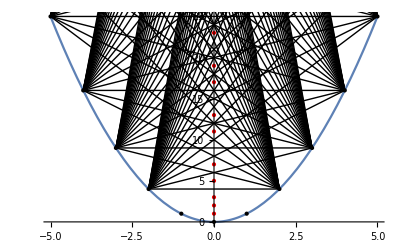

```mathematica
n=25;
f[x_]:=x^2;
P=Point[Table[{k,k^2},{k,-n,n}]];
L=Table[Line[{{i,i^2},{j,j^2}}],{i,-n,-2},{j,2,n}];
R=Point[Table[{0,Prime[k]},{k,1,n}]];
Plot[f[x],{x,-Sqrt[n],Sqrt[n]},Epilog->{P,L,{PointSize[Large],Red,R},{PointSize[Large],Red,Point[{0,1}]}}]
```